# Final Boat Calculations

### Clearing Variables

```mathematica
Clear["Global`*"]
```

### Defining Variables

```mathematica
f = (1/8)*x^2;
density =(28/1000);
ballastmass = 1000.;
xmin1 = -8.;
xmax1 = 8.;
ymin1 = 0.;
ymax1 = 8.;
zmin1 = 0.;
zmax1 =26.;
xballast = 0.;
yballast = (1/2);
xmast = 0.;
ymast = (51/2);
mastmass = 97.;
θ = 30.;
```

### Calculating Mass and Center of Mass

```mathematica
MassFunc[f_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,ballastmass_,xballast_,yballast_,density_,xmast_, ymast_,mastmass_]:=Module[{},
boat = ImplicitRegion[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}];

boatmass = zmax1*Integrate[density,{x, y}∈boat];

totalmass = boatmass+ballastmass;

xcomboat = ( 1/boatmass)*zmax1*Integrate[x*density,{x, y}∈boat];

ycomboat=(583/100);

xcom = 1/(totalmass)*(xcomboat*boatmass+xballast*ballastmass);

ycom = 1/(totalmass)*(ycomboat*boatmass+yballast*ballastmass+ymast*mastmass);

com = {xcom,ycom,0};

{boat,com, totalmass}
]
```

```mathematica
MassFunc[f,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,ballastmass,xballast,yballast,density,xmast,ymast,mastmass]
```

{ImplicitRegion[x^2/8<y<8.&&-8.<x<8.&&0.<y<8.,{x,y}],{0.,3.14057,0},1062.12}

### Function/Module

```mathematica
TorqueFunc[f_,density_,ballastmass_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,xballast_,yballast_,θ_, boat_, com_] := Module[{}, 
water = ImplicitRegion[If[θ<90, y<Tan[θ Degree]*x+d, y>Tan[θ Degree]*x+d],{{x,-10,10},{y,-10,10}}];

submerged = RegionIntersection[boat, water];

displacement = 1*zmax1*RegionMeasure[submerged];

draft = N[d/.FindRoot[displacement==totalmass, {d, -20, 20},WorkingPrecision->10][[1]]];

cob = Append[RegionCentroid[submerged/.{d->draft}],0];

buoyancy = totalmass*98/10*{-Sin[ θ Degree],Cos[θ Degree],0};

torque = Cross[cob-com,buoyancy][[3]];

torque
]
```

### Testing Function

```mathematica
TorqueFunc[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]
```

21618.

### Plotting Results

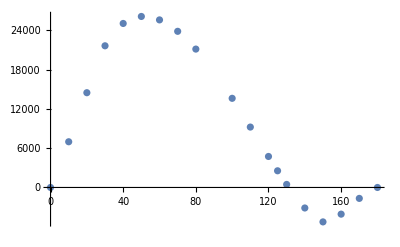

```mathematica
ListPlot[Table[{θ,TorqueFunc[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]},{θ,{0,10,20,30,40,50,60,70,80,100,110,120,125,130,140,150,160,170,180}}]]
```

### Visualizing Boat Shape

```mathematica
RegionPlot3D[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x, -10, 10},{y, 0, 20},{z, 0, 20}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

{{9.40017×10^-17,6.32509}}

{{0.,3.17276}}

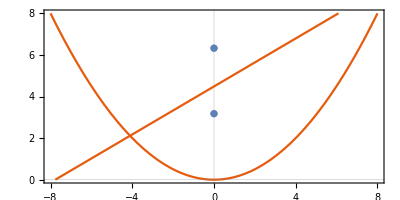

```mathematica
plotcob = {{cob[[1]],cob[[2]]}}
plotcom = {{com[[1]], com[[2]]}}
Show[Plot[f, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific", AspectRatio->Automatic],ListPlot[plotcob], ListPlot[plotcom],
Plot[Tan[30 Degree]*x+draft, {x,xmin1,xmax1},PlotRange->{{xmin1,xmax1},{ymin1,ymax1}}, PlotTheme->"Scientific"] , RegionPlot[submerged/.d->draft, {x,-8,8},{y,0,8}]]
```